### Construct data tables for )'( animation for Oscilloscope clock

Check data from original code, e.g. seconds hand

```mathematica
fromHexString[value_]:=Interpreter["HexInteger"][value];
```

```mathematica
secptr=fromHexString@{
"80","ec","80","80","ff","8b","ec","80","80","ff","96","ea","80","80","ff","a1","e7","80","80","ff",
"ab","e3","80","80","ff","b6","de","80","80","ff","bf","d8","80","80","ff","c8","d1","80","80","ff",
"d0","c9","80","80","ff","d7","c0","80","80","ff","dd","b6","80","80","ff","e2","ac","80","80","ff",
"e6","a2","80","80","ff","e9","97","80","80","ff","eb","8c","80","80","ff","eb","80","80","80","ff",
"eb","75","80","80","ff","e9","6a","80","80","ff","e6","5f","80","80","ff","e2","55","80","80","ff",
"dd","4a","80","80","ff","d7","41","80","80","ff","d0","38","80","80","ff","c8","30","80","80","ff",
"bf","29","80","80","ff","b6","23","80","80","ff","ab","1e","80","80","ff","a1","1a","80","80","ff",
"96","17","80","80","ff","8b","15","80","80","ff","80","15","80","80","ff","74","15","80","80","ff",
"69","17","80","80","ff","5e","1a","80","80","ff","54","1e","80","80","ff","4a","23","80","80","ff",
"40","29","80","80","ff","37","30","80","80","ff","2f","38","80","80","ff","28","41","80","80","ff",
"22","4b","80","80","ff","1d","55","80","80","ff","19","5f","80","80","ff","16","6a","80","80","ff",
"14","75","80","80","ff","14","80","80","80","ff","14","8c","80","80","ff","16","97","80","80","ff",
"19","a2","80","80","ff","1d","ac","80","80","ff","22","b6","80","80","ff","28","c0","80","80","ff",
"2f","c9","80","80","ff","37","d1","80","80","ff","40","d8","80","80","ff","49","de","80","80","ff",
"54","e3","80","80","ff","5e","e7","80","80","ff","69","ea","80","80","ff","74","ec","80","80","ff"};
```

```mathematica
lines=Partition[secptr,5]
```

{{128,236,128,128,255},{139,236,128,128,255},{150,234,128,128,255},{161,231,128,128,255},{171,227,128,128,255},{182,222,128,128,255},{191,216,128,128,255},{200,209,128,128,255},{208,201,128,128,255},{215,192,128,128,255},{221,182,128,128,255},{226,172,128,128,255},{230,162,128,128,255},{233,151,128,128,255},{235,140,128,128,255},{235,128,128,128,255},{235,117,128,128,255},{233,106,128,128,255},{230,95,128,128,255},{226,85,128,128,255},{221,74,128,128,255},{215,65,128,128,255},{208,56,128,128,255},{200,48,128,128,255},{191,41,128,128,255},{182,35,128,128,255},{171,30,128,128,255},{161,26,128,128,255},{150,23,128,128,255},{139,21,128,128,255},{128,21,128,128,255},{116,21,128,128,255},{105,23,128,128,255},{94,26,128,128,255},{84,30,128,128,255},{74,35,128,128,255},{64,41,128,128,255},{55,48,128,128,255},{47,56,128,128,255},{40,65,128,128,255},{34,75,128,128,255},{29,85,128,128,255},{25,95,128,128,255},{22,106,128,128,255},{20,117,128,128,255},{20,128,128,128,255},{20,140,128,128,255},{22,151,128,128,255},{25,162,128,128,255},{29,172,128,128,255},{34,182,128,128,255},{40,192,128,128,255},{47,201,128,128,255},{55,209,128,128,255},{64,216,128,128,255},{73,222,128,128,255},{84,227,128,128,255},{94,231,128,128,255},{105,234,128,128,255},{116,236,128,128,255}}

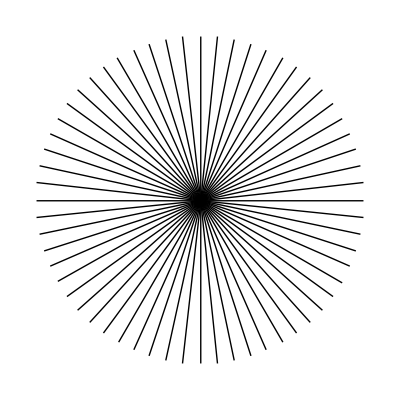

```mathematica
Graphics[Line[{{#[[1]],#[[2]]},{#[[3]],#[[4]]}}]&/@lines]
```

OK, that seems to work. Now construct a man (on paper) and rotate it

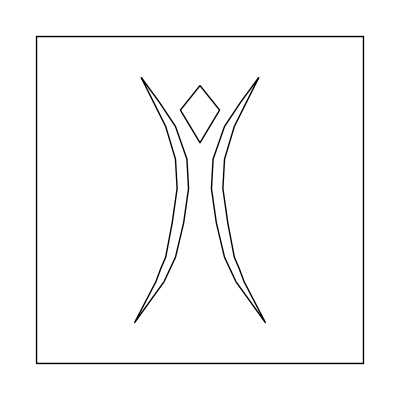

```mathematica
head={{0,70},{12,55},{0,35},{-12,55},{0,70}};body={{36,75},{25,60},{15,45},{8,25},{7,7},{10,-14},{15,-35},{22,-50},{40,-75},{27,-50},{24,-42},{21,-35},{17,-14},{14,7},{15,25},{21,45},{26,55},{36,75}};
Graphics[{Line[{{-100,-100},{-100,100},{100,100},{100,-100},{-100,-100}}],Line[head],Line[body],Line[#*{-1,1}&/@body]}]
```

```mathematica
rotate[point_,angle_]:={{Cos[angle],Sin[angle]},{-Sin[angle],Cos[angle]}}.point
```

```mathematica
Animate[Graphics[{Line[{{-100,-100},{-100,100},{100,100},{100,-100},{-100,-100}}],Line[rotate[#,angle]&/@head],Line[rotate[#,angle]&/@body],Line[rotate[#,angle]&/@(#*{-1,1}&/@body)]}],{angle,0,2π,π/30}]
```

```mathematica
data=Table[Flatten[Round[
{rotate[#,angle]&/@head,-128,rotate[#,angle]&/@body,-128,rotate[#,angle]&/@(#*{-1,1}&/@body),127}]]+128,{angle,0,2π,π/30}];
```

```mathematica
{Length[data],Length[data[[1]]]}
```

{61,85}

```mathematica
data>>"DataTableBM.h"
```

And a signature!

```mathematica
twelve=fromHexString@{"7a","eb","7a","d9","00","80","e8","83","eb","89","eb","8c","e8","8c","e5","80","d9","8c","d9","00"}
```

{122,235,122,217,0,128,232,131,235,137,235,140,232,140,229,128,217,140,217,0}

```mathematica
Graphics[{Line[{{122,235},{122,217}}],Line[Partition[{128,232,131,235,137,235,140,232,140,229,128,217,140,217},2]]}]
```

-Graphics-

```mathematica
Graphics[{Line[Partition[{5,9,4,10,2,10,1,9,1,8,2,7,4,7,5,6,5,5,4,4,2,4},2]],Line[{{1.5,7.5},{1,7},{1,1}}],Line[{{5,1},{1,5}}]}]
```

-Graphics-

```mathematica
Plus[#,{243,0}]&/@Partition[2*Flatten[{{5,9,4,10,2,10,1,9,1,8,2,7,4,7,5,6,5,5,4,4,2,4},{x,xx},{{1.5,7.5},{1,7},{1,1}},{x,xx},{{5,1},{1,5}}}],2]//Flatten//Round
```

{253,18,251,20,247,20,245,18,245,16,247,14,251,14,253,12,253,10,251,8,247,8,Round[243+2 x],Round[2 xx],246,15,245,14,245,2,Round[243+2 x],Round[2 xx],253,2,245,10}